```mathematica
?Eigenvalues
```

RowBox[{"Eigenvalues", "[", StyleBox["m", "TI"], "]"}] gives a list of the eigenvalues of the square matrix StyleBox["m", "TI"]. 
RowBox[{"Eigenvalues", "[", RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["a", "TI"]}], "}"}], "]"}] gives the generalized eigenvalues of StyleBox["m", "TI"] with respect to StyleBox["a", "TI"]. 
RowBox[{"Eigenvalues", "[", RowBox[{StyleBox["m", "TI"], ",", StyleBox["k", "TI"]}], "]"}] gives the first StyleBox["k", "TI"] eigenvalues of StyleBox["m", "TI"]. 
RowBox[{"Eigenvalues", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["a", "TI"]}], "}"}], ",", StyleBox["k", "TI"]}], "]"}] gives the first StyleBox["k", "TI"] generalized eigenvalues.

```mathematica
a=({{I, 1}, {0, I}})
```

{{ⅈ,1},{0,ⅈ}}

```mathematica
{{0,-ⅈ},{ⅈ,0}}//MatrixForm
```

(0 | -ⅈ
ⅈ | 0)

```mathematica
Eigenvalues[a]
```

{ⅈ,ⅈ}

```mathematica
{1/2 ⅈ (1+√5),-1/2 ⅈ (-1+√5)}//FullSimplify
```

{1/2 ⅈ (1+√5),-1/2 ⅈ (-1+√5)}

```mathematica
{1/2 ((1+ⅈ)-√(-4-2 ⅈ)),1/2 ((1+ⅈ)+√(-4-2 ⅈ))}//FullSimplify
```

{1/2 ((1+ⅈ)-√(-4-2 ⅈ)),1/2 ((1+ⅈ)+√(-4-2 ⅈ))}

```mathematica
1-1/4-1/36
```

13/18

```mathematica
-1/4-5/36
```

-7/18

```mathematica
(13/18)^2+(-5/18)^2+(-1/3)^2+(-7/18)^2
```

31/36

```mathematica
%//Sqrt
```

(√31)/6

```mathematica
Norm[({{13/18}, {-5/18}, {-1/3}, {1/9}})]
```

(√(13/2))/3

```mathematica
v4=({{0}, {1}, {0}, {0}})
u3=(6/Sqrt[31])*({{13/18}, {-5/18}, {-1/3}, {1/9}})
u2=(1/6)*({{1}, {1}, {3}, {5}})
u1=(1/2)*({{1}, {1}, {1}, {-1}})
```

{{0},{1},{0},{0}}

{{13/(3 √31)},{-5/(3 √31)},{-2/(√31)},{2/(3 √31)}}

{{1/6},{1/6},{1/2},{5/6}}

{{1/2},{1/2},{1/2},{-1/2}}

```mathematica
v3=({{1}, {0}, {0}, {0}})
```

```mathematica
({{1}, {0}, {0}, {0}})-1/4*({{1}, {1}, {1}, {-1}})-1/36*({{1}, {1}, {3}, {5}})
```

```mathematica
({{1}, {0}, {0}, {0}})-1/4*({{1}, {1}, {1}, {-1}})-1/36*({{1}, {1}, {3}, {5}})+5*Sqrt[2/403]*u3
```

```mathematica
{{583/558},{-2915/7254},{-583/1209},{583/3627}}//MatrixForm
```

```mathematica
v4'=({{583/558}, {-2915/7254}, {-583/1209}, {583/3627}})
```

{{583/558},{-2915/7254},{-583/1209},{583/3627}}

```mathematica
Norm[v4']
```

583/(93 √26)

```mathematica
{{13/18},{-5/18},{-1/3},{1/9}}//MatrixForm
```

```mathematica
u3'=({{13/18}, {-5/18}, {-1/3}, {1/9}})
```

{{13/18},{-5/18},{-1/3},{1/9}}

```mathematica
Norm[u3']
```

(√(13/2))/3

```mathematica
u3=(1/Norm[u3'])*u3
```

```mathematica
{{√(26/31)},{-5 √(2/403)},{-6 √(2/403)},{2 √(2/403)}}//MatrixForm
```

(√(26/31)
-5 √(2/403)
-6 √(2/403)
2 √(2/403))

```mathematica
Transpose[v4].u3
```

{{-5 √(2/403)}}

```mathematica
Transpose[v4]//MatrixForm
```

(0 | 1 | 0 | 0)

```mathematica
(Transpose[v4].u3)
```

{{-5/(3 √31)}}

```mathematica
u4=v4-(1/2)*u1-(1/6)*u2-(-5/(3*Sqrt[31]))*u3
```

{{-25/558},{353/558},{-41/93},{-287/558}}

```mathematica
%//MatrixForm
```

```mathematica
t44=({{-25/558}, {353/558}, {-41/93}, {-287/558}})
```

{{-25/558},{353/558},{-41/93},{-287/558}}

```mathematica
({{-5/18-(13 √31)/108}, {13/18+(5 √31)/108}, {-1/3+(√31)/18}, {-7/18+(7 √31)/108}})//FullSimplify
```

```mathematica
{{1/108 (-30-13 √31)},{1/108 (78+5 √31)},{1/18 (-6+√31)},{7/108 (-6+√31)}}//MatrixForm
```

```mathematica
t4=({{1/108 (-30-13 √31)}, {1/108 (78+5 √31)}, {1/18 (-6+√31)}, {7/108 (-6+√31)}})
```

{{1/108 (-30-13 √31)},{1/108 (78+5 √31)},{1/18 (-6+√31)},{7/108 (-6+√31)}}

```mathematica
Norm[t44]//FullSimplify
```

(√31)/6

```mathematica
?Norm
```

Norm[expr] gives the norm of a number, vector or matrix. 
Norm[expr,p] gives the p-norm.

```mathematica
u4=v4-(Flatten[Transpose[v4].u1])*u1-(Flatten[Transpose[v4].u2])*u2-(Flatten[Transpose[v4].u3])*u3
```

Thread::tdlen: Objects of unequal length in {1/2}\ {{1/2}, {1/2}, {1/2}, {1/2}} cannot be combined.

Thread::tdlen: Objects of unequal length in -{1/2}\ {{1/2}, {1/2}, {1/2}, {1/2}} cannot be combined.

Thread::tdlen: Objects of unequal length in {1/6}\ {{1/6}, {1/6}, {1/2}, {5/6}} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

{{-{1/6} {{1/6},{1/6},{1/2},{5/6}}-{1/2} {{1/2},{1/2},{1/2},{1/2}}-{-(5 √31)/54} {{(13 √31)/54},{-(5 √31)/54},{-(√31)/9},{-(7 √31)/54}}},{1-{1/6} {{1/6},{1/6},{1/2},{5/6}}-{1/2} {{1/2},{1/2},{1/2},{1/2}}-{-(5 √31)/54} {{(13 √31)/54},{-(5 √31)/54},{-(√31)/9},{-(7 √31)/54}}},{-{1/6} {{1/6},{1/6},{1/2},{5/6}}-{1/2} {{1/2},{1/2},{1/2},{1/2}}-{-(5 √31)/54} {{(13 √31)/54},{-(5 √31)/54},{-(√31)/9},{-(7 √31)/54}}},{-{1/6} {{1/6},{1/6},{1/2},{5/6}}-{1/2} {{1/2},{1/2},{1/2},{1/2}}-{-(5 √31)/54} {{(13 √31)/54},{-(5 √31)/54},{-(√31)/9},{-(7 √31)/54}}}}

```mathematica
Clear[a,b,c,t,u]
```

```mathematica
a=(1/7)*({{2, 3, 6}, {3, -6, 2}, {6, 2, -3}})
```

{{2/7,3/7,6/7},{3/7,-6/7,2/7},{6/7,2/7,-3/7}}

```mathematica
CharacteristicPolynomial[a,T]
```

1+T-T^2-T^3

```mathematica
%//Simplify
```

-(-1+T) (1+T)^2

```mathematica
NullSpace[a-IdentityMatrix[3]]
```

{{3/2,1/2,1}}

```mathematica
Norm[({{3/2}, {1/2}, {1}})]
```

√(7/2)

```mathematica
a.Transpose[a]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Det[t*IdentityMatrix[3]-a]
```

```mathematica
-1-t+t^2+t^3//FullSimplify
```

(-1+t) (1+t)^2

```mathematica
(a-IdentityMatrix[3]).(a+IdentityMatrix[3])
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
NullSpace[a-IdentityMatrix[3]]
```

```mathematica
RowReduce[{{3/2,1/2,1}}]
```

{{1,1/3,2/3}}

```mathematica
%//MatrixForm
```

(3/2 | 1/2 | 1)

```mathematica
Clear[u1,u2,u3]
```

```mathematica
u1=({{3}, {1}, {2}})
```

{{3},{1},{2}}

```mathematica
u2=({{-2}, {0}, {3}})
```

{{-2},{0},{3}}

```mathematica
u3=({{-1}, {3}, {0}})
```

{{-1},{3},{0}}

```mathematica
Norm[u1]
```

√14

```mathematica
p=({{3/√14, -2/√13, -1/√10}, {1/√14, 0, 3/√10}, {2/√14, 3/√13, 0}})
```

{{3/(√14),-2/(√13),-1/(√10)},{1/(√14),0,3/(√10)},{√(2/7),3/(√13),0}}

```mathematica
Transpose[p].a.p//MatrixForm
```

(2/7+(3 ((9 √(2/7))/7+3/(7 √14)))/(√14)+(-(√(2/7))/7+9/(7 √14))/(√14) | 3 √(2/91)-(2 ((9 √(2/7))/7+3/(7 √14)))/(√13) | -((9 √(2/7))/7+3/(7 √14))/(√10)+(3 (-(√(2/7))/7+9/(7 √14)))/(√10)
0 | -1 | -√(2/65)
(-(9 √(2/5))/7-3/(7 √10))/(√14)+(3 (-(√(2/5))/7+9/(7 √10)))/(√14) | -(2 (-(√(2/5))/7+9/(7 √10)))/(√13) | (3 (-(9 √(2/5))/7-3/(7 √10)))/(√10)-(-(√(2/5))/7+9/(7 √10))/(√10))

```mathematica
NullSpace[a+IdentityMatrix[3]]
```

{{-2/3,0,1},{-1/3,1,0}}

```mathematica
Clear[a,b,c,d,e,f,g]
```

```mathematica
pges=({{3/√14, 1/√10, x3}, {1/√14, -3/√10, x6}, {2/√14, 0, x9}})
```

{{3/(√14),1/(√10),x3},{1/(√14),-3/(√10),x6},{√(2/7),0,x9}}

```mathematica
p=({{3/√14, 1/√10, 3/√35}, {1/√14, -3/√10, 1/√35}, {2/√14, 0, -5/√35}})
```

```mathematica
pt=Transpose[p]
```

```mathematica
a.p
```

```mathematica
pt.{{(9 √(2/7))/7+3/(7 √14),(√(2/5))/7-9/(7 √10),-(6 √(5/7))/7+9/(7 √35)},{-(√(2/7))/7+9/(7 √14),(9 √(2/5))/7+3/(7 √10),-(2 √(5/7))/7+3/(7 √35)},{√(2/7),0,√(5/7)}}
```

{{2/7+(3 ((9 √(2/7))/7+3/(7 √14)))/(√14)+(-(√(2/7))/7+9/(7 √14))/(√14),(3 ((√(2/5))/7-9/(7 √10)))/(√14)+((9 √(2/5))/7+3/(7 √10))/(√14),(√10)/7+(-(2 √(5/7))/7+3/(7 √35))/(√14)+(3 (-(6 √(5/7))/7+9/(7 √35)))/(√14)},{((9 √(2/7))/7+3/(7 √14))/(√10)-(3 (-(√(2/7))/7+9/(7 √14)))/(√10),((√(2/5))/7-9/(7 √10))/(√10)-(3 ((9 √(2/5))/7+3/(7 √10)))/(√10),-(3 (-(2 √(5/7))/7+3/(7 √35)))/(√10)+(-(6 √(5/7))/7+9/(7 √35))/(√10)},{-(√10)/7+(3 ((9 √(2/7))/7+3/(7 √14)))/(√35)+(-(√(2/7))/7+9/(7 √14))/(√35),(3 ((√(2/5))/7-9/(7 √10)))/(√35)+((9 √(2/5))/7+3/(7 √10))/(√35),-5/7+(-(2 √(5/7))/7+3/(7 √35))/(√35)+(3 (-(6 √(5/7))/7+9/(7 √35)))/(√35)}}

```mathematica
{{3/(√14),1/(√14),√(2/7)},{1/(√10),-3/(√10),0},{3/(√35),1/(√35),-√(5/7)}}//MatrixForm
```

```mathematica
({{3/(√14), 1/(√14), √(2/7)}, {1/(√10), -3/(√10), 0}, {3/(√35), 1/(√35), -√(5/7)}}).({{2/7, 3/7, 6/7}, {3/7, -6/7, 2/7}, {6/7, 2/7, -3/7}}).({{3/√14, 1/√10, 3/√35}, {1/√14, -3/√10, 1/√35}, {2/√14, 0, -5/√35}})
```

{{2/7+(3 ((9 √(2/7))/7+3/(7 √14)))/(√14)+(-(√(2/7))/7+9/(7 √14))/(√14),((9 √(2/7))/7+3/(7 √14))/(√10)-(3 (-(√(2/7))/7+9/(7 √14)))/(√10),-(√10)/7+(3 ((9 √(2/7))/7+3/(7 √14)))/(√35)+(-(√(2/7))/7+9/(7 √14))/(√35)},{(3 ((√(2/5))/7-9/(7 √10)))/(√14)+((9 √(2/5))/7+3/(7 √10))/(√14),((√(2/5))/7-9/(7 √10))/(√10)-(3 ((9 √(2/5))/7+3/(7 √10)))/(√10),(3 ((√(2/5))/7-9/(7 √10)))/(√35)+((9 √(2/5))/7+3/(7 √10))/(√35)},{(√10)/7+(-(2 √(5/7))/7+3/(7 √35))/(√14)+(3 (-(6 √(5/7))/7+9/(7 √35)))/(√14),-(3 (-(2 √(5/7))/7+3/(7 √35)))/(√10)+(-(6 √(5/7))/7+9/(7 √35))/(√10),-5/7+(-(2 √(5/7))/7+3/(7 √35))/(√35)+(3 (-(6 √(5/7))/7+9/(7 √35)))/(√35)}}

```mathematica
RowReduce[({{3, 1, 2}, {1, -3, 0}})]
```

{{1,0,3/5},{0,1,1/5}}

```mathematica
√(5/7)==5/√35
```

True

```mathematica
Solve[Transpose[pges].a.pges==({{1, 0, 0}, {0, -1, 0}, {0, 0, -1}})]
```

{{x9→-√(5/7),x3→3/(√35),x6→1/(√35)},{x9→√(5/7),x3→-3/(√35),x6→-1/(√35)}}

```mathematica
Solve[IdentityMatrix[3].({{x1}, {x2}, {x3}})==0]
```

{{x1→0,x2→0,x3→0}}

```mathematica
RowReduce[({{3, 1, 2}, {-2, 0, 3}, {-1, 3, 0}})]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
%//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Norm[u3]
```

(√13)/3

```mathematica
Eigenvalues[a]
```

{-1,-1,1}

```mathematica
Eigensystem[a]
```

{{-1,-1,1},{{-2/3,0,1},{-1/3,1,0},{3/2,1/2,1}}}

```mathematica
%//MatrixForm
```

(-1 | -1 | 1
{-2/3,0,1} | {-1/3,1,0} | {3/2,1/2,1})

```mathematica
?Eigensystem
```

Eigensystem[m] gives a list {values,vectors} of the eigenvalues and eigenvectors of the square matrix m. 
Eigensystem[{m,a}] gives the generalized eigenvalues and eigenvectors of m with respect to a. 
Eigensystem[m,k] gives the eigenvalues and eigenvectors for the first k eigenvalues of m. 
Eigensystem[{m,a},k] gives the first k generalized eigenvalues and eigenvectors.

```mathematica
?NullSpace
```

NullSpace[m] gives a list of vectors that forms a basis for the null space of the matrix m.

```mathematica
NullSpace[a-IdentityMatrix[3]]
```

{{3/2,1/2,1}}

```mathematica
NullSpace[a+IdentityMatrix[3]]
```

{{-2/3,0,1},{-1/3,1,0}}

```mathematica
%//MatrixForm
```

(3/2 | 1/2 | 1)

```mathematica
RowReduce[a-IdentityMatrix[3]]
```

{{1,0,-3/2},{0,1,-1/2},{0,0,0}}

```mathematica
%//MatrixForm
```

(1 | 0 | -3/2
0 | 1 | -1/2
0 | 0 | 0)

```mathematica
?MinimalPolynomial
```

MinimalPolynomial[s,x] gives the minimal polynomial in x for which the algebraic number s is a root.

```mathematica
MinimalPolynomial[a,t]
```

{{-2+7 t,-3+7 t,-6+7 t},{-3+7 t,6+7 t,-2+7 t},{-6+7 t,-2+7 t,3+7 t}}

```mathematica
a1=({{1/3}, {-1}, {0}})
```

{{1/3},{-1},{0}}

```mathematica
a2=({{2/3}, {0}, {-1}})
```

{{2/3},{0},{-1}}

```mathematica
a1.Transpose[a1]
```

{{1/9,-1/3,0},{-1/3,1,0},{0,0,0}}

```mathematica
Norm[a1]
```

(√10)/3

```mathematica
a3=({{3}, {1}, {2}})
```

{{3},{1},{2}}

```mathematica
Norm[a2]
```

(√13)/3

```mathematica
p=({{3/Sqrt[14], 3/(3*Sqrt[14]), 6/(3*√3)}, {1/Sqrt[14], -3/√14, 0}, {2/Sqrt[14], 0, -3/√13}})
```

{{3/(√14),1/(√14),2/(√3)},{1/(√14),-3/(√14),0},{√(2/7),0,-3/(√13)}}

```mathematica
Transpose[p].a.p
```

{{2/7+(3 ((9 √(2/7))/7+3/(7 √14)))/(√14)+(-(√(2/7))/7+9/(7 √14))/(√14),((9 √(2/7))/7+3/(7 √14))/(√14)-(3 (-(√(2/7))/7+9/(7 √14)))/(√14),-3 √(2/91)+(2 ((9 √(2/7))/7+3/(7 √14)))/(√3)},{(3 ((√(2/7))/7-9/(7 √14)))/(√14)+((9 √(2/7))/7+3/(7 √14))/(√14),((√(2/7))/7-9/(7 √14))/(√14)-(3 ((9 √(2/7))/7+3/(7 √14)))/(√14),(2 ((√(2/7))/7-9/(7 √14)))/(√3)},{(3 (4/(7 √3)-18/(7 √13)))/(√14)+((2 √3)/7-6/(7 √13))/(√14)+√(2/7) ((4 √3)/7+9/(7 √13)),(4/(7 √3)-18/(7 √13))/(√14)-(3 ((2 √3)/7-6/(7 √13)))/(√14),(2 (4/(7 √3)-18/(7 √13)))/(√3)-(3 ((4 √3)/7+9/(7 √13)))/(√13)}}

```mathematica
%//MatrixForm
```

(2/7+(3 ((9 √(2/7))/7+3/(7 √14)))/(√14)+(-(√(2/7))/7+9/(7 √14))/(√14) | ((9 √(2/7))/7+3/(7 √14))/(√14)-(3 (-(√(2/7))/7+9/(7 √14)))/(√14) | -3 √(2/91)+(2 ((9 √(2/7))/7+3/(7 √14)))/(√3)
(3 ((√(2/7))/7-9/(7 √14)))/(√14)+((9 √(2/7))/7+3/(7 √14))/(√14) | ((√(2/7))/7-9/(7 √14))/(√14)-(3 ((9 √(2/7))/7+3/(7 √14)))/(√14) | (2 ((√(2/7))/7-9/(7 √14)))/(√3)
(3 (4/(7 √3)-18/(7 √13)))/(√14)+((2 √3)/7-6/(7 √13))/(√14)+√(2/7) ((4 √3)/7+9/(7 √13)) | (4/(7 √3)-18/(7 √13))/(√14)-(3 ((2 √3)/7-6/(7 √13)))/(√14) | (2 (4/(7 √3)-18/(7 √13)))/(√3)-(3 ((4 √3)/7+9/(7 √13)))/(√13))

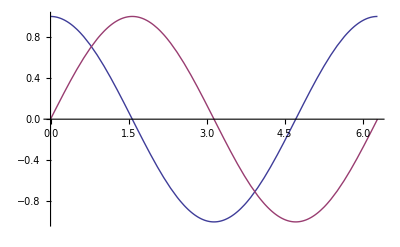

```mathematica
Plot[{Cos[x],Sin[x]},{x,0,2 π}]
```

```mathematica
-Sin[π/2]
```

-1

```mathematica
1/4-5/36
```

1/9